#### functions

```mathematica
connectivityEI[totN_,eR_,means_,gains_]:=If[Or[eR==0,eR==1],
Table[RandomVariate[NormalDistribution[means,gains/Sqrt[totN]],totN],totN],
Module[{eN=Round[eR*totN],iN,meanEE,meanEI,meanIE,meanII},
iN=totN-eN;
If[Length[means]==1,
meanEE=means[[1]];meanEI=-meanEE*eN/iN;meanIE=meanEE;meanII=meanEI,
If[Length[means]==2,
meanEE=means[[1]];meanEI=-meanEE*eN/iN;meanIE=means[[2]];meanII=-meanIE*eN/iN,
If[Length[means]==4,
meanEE=means[[1]];meanEI=means[[2]];meanIE=means[[3]];meanII=means[[4]],]]];
Return[ArrayFlatten[{{Table[RandomVariate[NormalDistribution[meanEE,gains[[1,1]]/Sqrt[(*eN*)totN]],eN],eN],Table[RandomVariate[NormalDistribution[meanEI,gains[[1,2]]/Sqrt[(*iN*)totN]],iN],eN]},{Table[RandomVariate[NormalDistribution[meanIE,gains[[2,1]]/Sqrt[(*eN*)totN]],eN],iN],Table[RandomVariate[NormalDistribution[meanII,gains[[2,2]]/Sqrt[(*iN*)totN]],iN],iN]}}]]]]
```

```mathematica
rk4OdeSolver[velocities_,initials_,domain_,resolution_]:=Module[{positionsOutput=Table[Table[0,Length[initials]],(domain[[2]]-domain[[1]])*resolution+1],positionsPresent=initials,positionsNext,correction1,correction2,correction3,correction4,stepSize=1/resolution},
positionsOutput[[1]]=initials;
Do[correction1=velocities[positionsPresent];
correction2=velocities[positionsPresent+stepSize*correction1/2];
correction3=velocities[positionsPresent+stepSize*correction2/2];
correction4=velocities[positionsPresent+stepSize*correction3];
positionsNext=positionsPresent+stepSize*(correction1/6+correction2/3+correction3/3+correction4/6);
positionsOutput[[idx+1]]=positionsNext;
positionsPresent=positionsNext,
{idx,(domain[[2]]-domain[[1]])*resolution}];
positionsOutput=Transpose[positionsOutput];
Return[positionsOutput]
]
rk4OdeXSolver[velocities_,externals_,initials_,domain_,resolution_]:=
Module[{velocities4,initials4,dimN=Length[initials]},
velocities4[positions4_]:=Join[velocities[positions4[[1;;dimN]]]+externals[positions4[[dimN+1]]],{1}];
initials4=Join[initials,{domain[[1]]}];
Return[rk4OdeSolver[velocities4,initials4,domain,resolution][[1;;dimN]]]]
```

```mathematica
crossCorrelationMoment[list1_,list2_,lag_]:=Module[{mean1=Mean[list1],mean2=Mean[list2]},Return[list1[[1;;Length[list1]-lag]].list2[[lag+1;;Length[list2]]]/Sqrt[Total[Norm[list1]^2]]/Sqrt[Total[Norm[list2]^2]]]]
crossCorrelationCumulant[list1_,list2_,lag_]:=Module[{mean1=Mean[list1],mean2=Mean[list2]},Return[(list1[[1;;Length[list1]-lag]]-mean1).(list2[[lag+1;;Length[list2]]]-mean2)/Sqrt[Total[Norm[list1-mean1]^2]]/Sqrt[Total[Norm[list2-mean2]^2]]]]
(*With[{foo=Table[Exp[-idx],{idx,0,10}]},
ListPlot[{Table[{lag,crossCorrelationMoment[foo,foo,lag]},{lag,0,10}],Table[{lag,crossCorrelationCumulant[foo,foo,lag]},{lag,0,10}]}]]*)
```

```mathematica
participationRatio[list_]:=Mean[list]^2/Mean[list^2]
```

```mathematica
save[expression_,filename_]:=Module[{imported},Export[StringJoin[NotebookDirectory[],filename,".mx"],expression];imported=Import[StringJoin[NotebookDirectory[],filename,".mx"]];
If[imported==expression,Print[StringJoin["saved to ",filename]]]]
```

#### 1 instance details

```mathematica
totN=100;
eR=0.8;
means={0.18};
gains=Table[5.,2];
connectivity=connectivityEI[totN,eR,means,Table[gains,2]];
externalR=0.2;
connectivityExternal=RandomVariate[BernoulliDistribution[externalR],totN]*1.;
freq=8/50;
timeI={0,50};
externalStrength=5.;
```

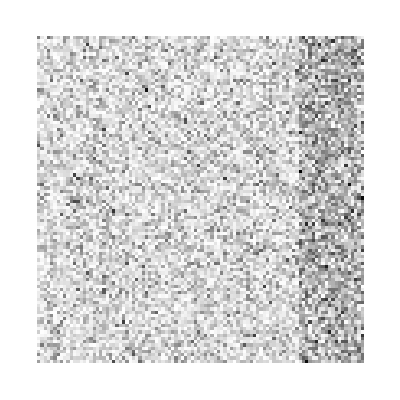
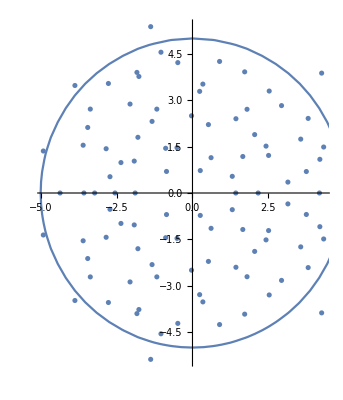

```mathematica
{ArrayPlot[connectivity],Show[ComplexListPlot[Eigenvalues[connectivity]],ContourPlot[x^2+y^2==(eR*gains[[1]]^2+(1-eR)*gains[[2]]^2),{x,-10,10},{y,-10,10}]]}
```

```mathematica
nonlinearity1=Identity;
nonlinearity2=(*With[{r=0.1},Function[x,If[x>0,(2-r)Tanh[x/(2-r)],r*Tanh[x/r]]]]*)Tanh;
velocities[positions_]:=-positions+nonlinearity1[connectivity.nonlinearity2[positions]];
spikeTimes=Sort[RandomVariate[UniformDistribution[timeI],Round[(timeI[[2]]-timeI[[1]])*freq]]];
externals[time_]:=connectivityExternal*externalStrength*Total[Exp[-(time-spikeTimes)^2/2/0.5^2]];
resolution=24(*60*);
initials=RandomVariate[NormalDistribution[0,1],totN]+Table[0.,{idx,totN}];states=nonlinearity2[rk4OdeXSolver[velocities,externals,initials,timeI,resolution]];
```

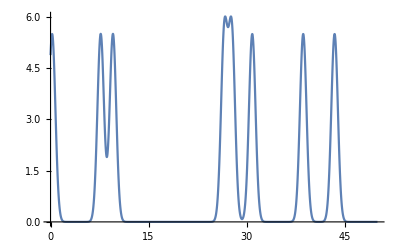
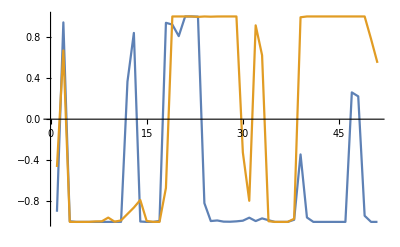

```mathematica
characteristicIdxs={Position[connectivityExternal,0.][[1,1]],Position[connectivityExternal,1.][[1,1]]};
(*statesA=Table[Table[states[[idx,time*resolution+1]],{time,0,timeI[[2]]-timeI[[1]](*,1/resolution*)}],{idx,characteristicIdxs}];*)
statesA=states[[characteristicIdxs,Table[time*resolution+1,{time,0,timeI[[2]]-timeI[[1]](*,1/resolution*)}]]];
{Plot[Mean[externals[time]]/externalR,Join[{time},timeI],PlotRange->All],ListPlot[statesA,Joined->True,PlotRange->All]}
```

```mathematica
acs=Table[Table[{lag,crossCorrelationMoment[states[[idx]],states[[idx]],lag*resolution]},{lag,0,timeI[[2]]-timeI[[1]](*,Floor[(timeI[[2]]-timeI[[1]])/100]*)}],{idx,totN}];
popMeanAc=Map[Mean,Transpose[acs]];
```

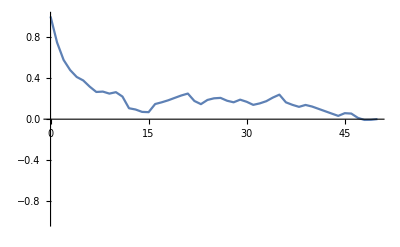
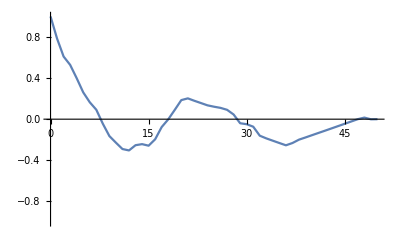

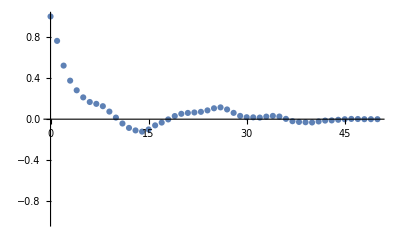

```mathematica
Table[ListPlot[acs[[idx]],Joined->True,PlotRange->{-1,1}],{idx,characteristicIdxs}]
(*Table[ListLogLogPlot[Abs[acs[[idx]]],Joined->True,PlotRange->{-1,1}],{idx,characteristicIdxs}]*)
ListPlot[popMeanAc,PlotRange->{-1,1}]
```

```mathematica
ccs=Table[Table[{lag,crossCorrelationMoment[states[[1]],states[[idx]],lag*resolution]},{lag,0,timeI[[2]]-timeI[[1]],1}],{idx,totN}];
```

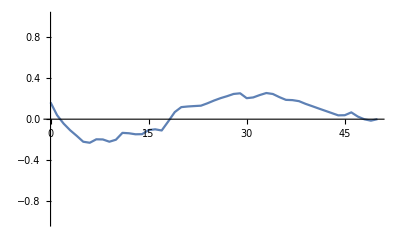
{-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[ccs[[idx]],Joined->True,PlotRange->{-1,1}],{idx,characteristicIdxs}]
```

```mathematica
pcs=Transpose[PrincipalComponents[Transpose[states]]];
vars=Map[Variance,pcs];
pr=participationRatio[vars];
(*With[{foo=Map[Variance,Transpose[PrincipalComponents[Transpose[states]]]],bar=Eigenvalues[Table[(states[[idx1]]-Mean[states[[idx1]]]).(states[[idx2]]-Mean[states[[idx2]]]),{idx1,totN},{idx2,totN}]]},
ListPlot[bar/foo,PlotRange->All]]*)
```

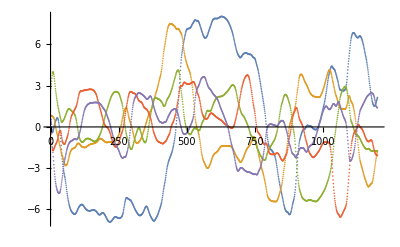

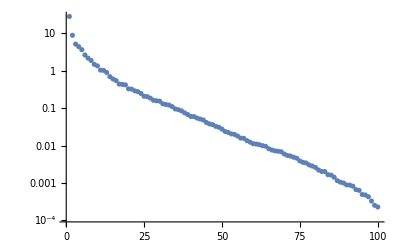
{-Graphics-,0.0514739}

```mathematica
ListPlot[pcs[[1;;Round[pr*totN]]],PlotRange->All]
{ListLogPlot[vars,PlotRange->All],pr}
```

#### J average - free

```mathematica
totN=100(*300*);
eR=0.8;
means={0.18};
gains=Table[5.,2];
timeI={0,50};
resolution=24(*60*);
nonlinearity1=Identity;
nonlinearity2=(*With[{r=0.1},Function[x,If[x>0,(2-r)Tanh[x/(2-r)],r*Tanh[x/r]]]]*)Tanh;
instanceN=100;
popMeanAcs=Table[Table[0,{lag,0,timeI[[2]]-timeI[[1]]}],instanceN];
prs=Table[0,instanceN];
Do[connectivity=connectivityEI[totN,eR,means,Table[gains,2]];
velocities[positions_]:=-positions+nonlinearity1[connectivity.nonlinearity2[positions]];
initials=RandomVariate[NormalDistribution[0,1],totN]+Table[0.,{idx,totN}];states=nonlinearity2[rk4OdeSolver[velocities,initials,timeI,resolution]];
acsT=Table[Table[{lag,crossCorrelationMoment[states[[idx]],states[[idx]],lag*resolution]},{lag,0,timeI[[2]]-timeI[[1]],1}],{idx,totN}];
popMeanAcs[[instanceIdx]]=Map[Mean,Transpose[acsT]];
prs[[instanceIdx]]=participationRatio[Map[Variance,Transpose[PrincipalComponents[Transpose[states]]]]],{instanceIdx,instanceN}]
```

```mathematica
meanAc=Map[Mean,Transpose[popMeanAcs]];
meanPr=Mean[prs];
```

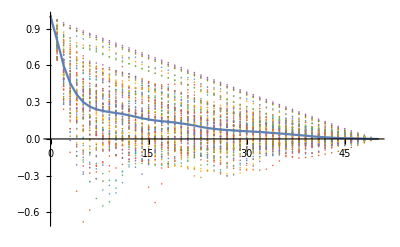
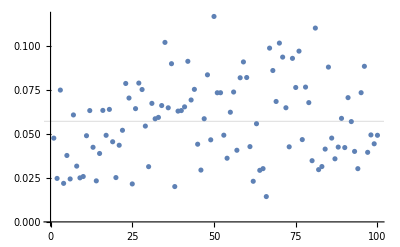

```mathematica
{Show[ListPlot[popMeanAcs,PlotRange->All],ListPlot[meanAc,PlotRange->All,Joined->True]],ListPlot[prs,GridLines->{{}, {meanPr}}]}
```

#### J average - under external inputs

```mathematica
totN=100(*300*);
eR=0.8;
means={0.18};
gains=Table[5.,2];
externalRs={0.2,0.8};
freqs={8,24}/50;
externalStrengths={1,10,40};
timeI={0,50};
resolution=24(*60*);
nonlinearity1=Identity;
nonlinearity2=(*With[{r=0.1},Function[x,If[x>0,(2-r)Tanh[x/(2-r)],r*Tanh[x/r]]]]*)Tanh;
instanceN=20(*100*);
popMeanAcs=Table[Table[Table[Table[Table[0,{lag,0,timeI[[2]]-timeI[[1]]}],instanceN],Length[externalStrengths]],Length[freqs]],Length[externalRs]];
prs=Table[Table[Table[Table[0,instanceN],Length[externalStrengths]],Length[freqs]],Length[externalRs]];
Do[connectivity=connectivityEI[totN,eR,means,Table[gains,2]];
velocities[positions_]:=-positions+nonlinearity1[connectivity.nonlinearity2[positions]];
Do[connectivityExternal=Join[RandomVariate[BernoulliDistribution[externalRs[[externalRIdx]]],Round[totN*eR]],Table[0,totN-Round[totN*eR]]]*1.;
Do[spikeTimes=Sort[RandomVariate[UniformDistribution[timeI],Round[(timeI[[2]]-timeI[[1]])*freqs[[freqIdx]]]]];
Do[externals[time_]:=connectivityExternal*(freqs[[1]]/freqs[[freqIdx]]*externalRs[[1]]/externalRs[[externalRIdx]]*externalStrengths[[externalStrengthIdx]])*Total[Exp[-(time-spikeTimes)^2/2/0.5^2]];
initials=RandomVariate[NormalDistribution[0,1],totN]+Table[0.,{idx,totN}];states=nonlinearity2[rk4OdeXSolver[velocities,externals,initials,timeI,resolution]];
acsT=Table[Table[{lag,crossCorrelationMoment[states[[idx]],states[[idx]],lag*resolution]},{lag,0,timeI[[2]]-timeI[[1]],1}],{idx,totN}];
popMeanAcs[[externalRIdx,freqIdx,externalStrengthIdx,instanceIdx]]=Map[Mean,Transpose[acsT]];
prs[[externalRIdx,freqIdx,externalStrengthIdx,instanceIdx]]=participationRatio[Map[Variance,Transpose[PrincipalComponents[Transpose[states]]]]],{externalStrengthIdx,Length[externalStrengths]}],{freqIdx,Length[freqs]}],{externalRIdx,Length[externalRs]}],{instanceIdx,instanceN}]
(*save[popMeanAcs,"popMeanAcs"]
save[prs,"prs"]*)
```

General::munfl: 0.25 4.21828×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.25 2.23144×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
meanAc=Table[Table[Table[Map[Mean,Transpose[popMeanAcs[[externalRIdx,freqIdx,externalStrengthIdx]]]],{externalStrengthIdx,Length[externalStrengths]}],{freqIdx,Length[freqs]}],{externalRIdx,Length[externalRs]}];
statsPr=Table[Table[Table[{Mean[prs[[externalRIdx,freqIdx,externalStrengthIdx]]],StandardDeviation[prs[[externalRIdx,freqIdx,externalStrengthIdx]]]},{externalStrengthIdx,Length[externalStrengths]}],{freqIdx,Length[freqs]}],{externalRIdx,Length[externalRs]}];
```

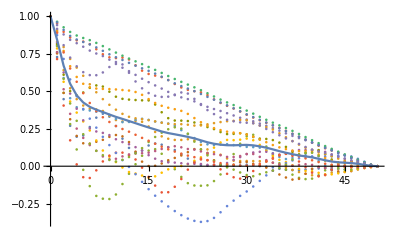
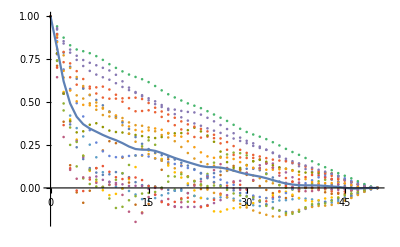
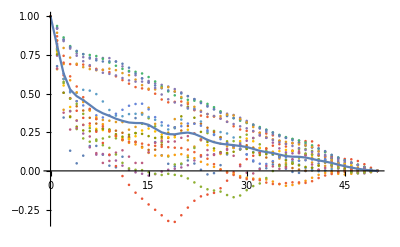
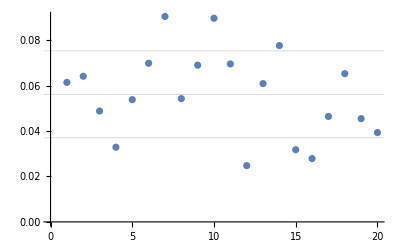
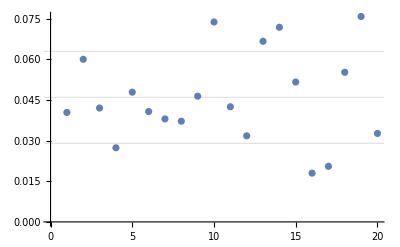
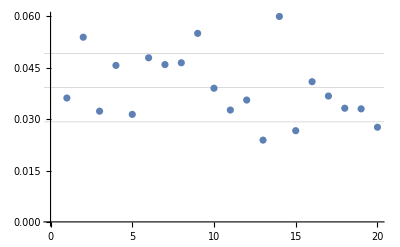
{ext R, freq, ext Str} | {0.8,4/25,1} | {0.8,4/25,10} | {0.8,4/25,40}
AC | -Graphics- | -Graphics- | -Graphics-
PR | -Graphics- | -Graphics- | -Graphics-

```mathematica
With[{externalRPlotIdxs={2},freqPlotIdxs={1},externalStrengthPlotIdxs={1,2,3}},
Grid[Transpose[Join[{{"{ext R, freq, ext Str}","AC","PR"}},
Flatten[Table[Table[Table[{{externalRs[[externalRIdx]],freqs[[freqIdx]],externalStrengths[[externalStrengthIdx]]},
Show[ListPlot[popMeanAcs[[externalRIdx,freqIdx,externalStrengthIdx]],PlotRange->All],ListPlot[meanAc[[externalRIdx,freqIdx,externalStrengthIdx]],PlotRange->All,Joined->True]],ListPlot[prs[[externalRIdx,freqIdx,externalStrengthIdx]],GridLines->{{}, statsPr[[externalRIdx,freqIdx,externalStrengthIdx,1]]+{-1,0,1}*statsPr[[externalRIdx,freqIdx,externalStrengthIdx,2]]}]},{externalStrengthIdx,externalStrengthPlotIdxs}],
{freqIdx,freqPlotIdxs}],
{externalRIdx,externalRPlotIdxs}],2]]]]]
```

#### classifiability - different freqs

```mathematica
totN=100(*300*);
eR=0.8;
means={0.18};
gains=Table[5.,2];
connectivity=connectivityEI[totN,eR,means,Table[gains,2]];
externalR=0.2;
connectivityExternal=RandomVariate[BernoulliDistribution[externalR],totN]*1.;
nonlinearity1=Identity;
nonlinearity2=(*With[{r=0.1},Function[x,If[x>0,(2-r)Tanh[x/(2-r)],r*Tanh[x/r]]]]*)Tanh;
velocities[positions_]:=-positions+nonlinearity1[connectivity.nonlinearity2[positions]];
freqs={8,16}/50;
externalStrength=5.;
timeI={0,50};
resolution=24(*60*);
instanceN=20(*100*);
statesLabeledAll=Table[Table[(Table[Table[0,(timeI[[2]]-timeI[[1]])*resolution+1],totN]->0),instanceN],Length[freqs]];
Do[spikeTimes=Sort[RandomVariate[UniformDistribution[timeI],Round[(timeI[[2]]-timeI[[1]])*freqs[[conditionIdx]]]]];
externals[time_]:=connectivityExternal*(freqs[[1]]/freqs[[conditionIdx]]*externalStrength)*Total[Exp[-(time-spikeTimes)^2/2/0.5^2]];
Do[initials=RandomVariate[NormalDistribution[0,1],totN]+Table[0.,{idx,totN}];statesLabeledAll[[conditionIdx,instanceIdx]]=(nonlinearity2[rk4OdeXSolver[velocities,externals,initials,timeI,resolution]]->freqs[[conditionIdx]])
,{instanceIdx,instanceN}],{conditionIdx,Length[freqs]}]
Print[StringJoin["spectral radius is ",ToString[Sqrt[eR*gains[[1]]^2+(1-eR)*gains[[2]]^2]]]]
(*save[{connectivity,connectivityExternal},"connectivities"]
save[statesLabeledAll,"statesLabeledAll"]*)
```

spectral radius is 5.

%diff between rms rates: 0.00130172

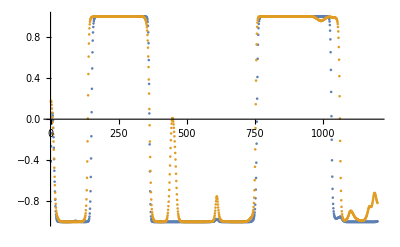
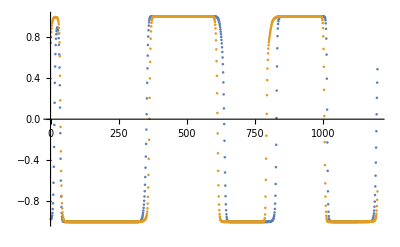

```mathematica
characteristicIdxs={Position[connectivityExternal,0.][[1,1]],Position[connectivityExternal,1.][[1,1]]};
With[{means=Table[Sqrt[Mean[Mean[Mean[statesLabeledAll[[conditionIdx,;;,1]]^2]]]],{conditionIdx,Length[freqs]}]},
With[{mean1=Max[means],mean2=Min[means]},Print[StringJoin["%diff between rms rates: ",ToString[2(mean1-mean2)/(mean1+mean2)]]]]]
Table[ListPlot[statesLabeledAll[[conditionIdx,1,1]][[characteristicIdxs]]],{conditionIdx,Length[freqs]}]
```

```mathematica
trainingInstanceN=Round[instanceN*0.5];
classifier=Classify[Flatten[statesLabeledAll[[;;,1;;trainingInstanceN]],1](*,Method->"SupportVectorMachine"*)];
testResults=Table[Table[{statesLabeledAll[[conditionIdx,instanceIdx,2]],classifier[statesLabeledAll[[conditionIdx,instanceIdx,1]]]},{instanceIdx,trainingInstanceN+1,instanceN}],{conditionIdx,Length[freqs]}];
```

```mathematica
errors=Table[Table[{freqs[[conditionIdx]],testResults[[conditionIdx,instanceIdx,2]]-testResults[[conditionIdx,instanceIdx,1]]},{instanceIdx,instanceN-trainingInstanceN}],{conditionIdx,Length[freqs]}];
errorRates=Table[{freqs[[conditionIdx]],Mean[Map[Function[x,Boole[x≠0]],errors[[conditionIdx,;;,2]]]]},{conditionIdx,Length[freqs]}];
```

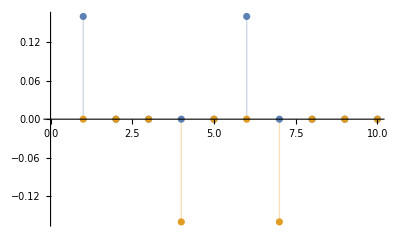
{Classifier information
Data type | NumericalTensor (size: ××1001201)
Classes | ,,4/258/25
Accuracy | (67.6.) %
Method | LogisticRegression
Single evaluation time | 2.17 s/example
Batch evaluation speed | 0.515 examples/s
Loss | 0.636 ± 0.051
Model memory | 51.6 MB
Training examples used | 20 examples
Training time | 1 38,class | %error
4/25 | 1/5
8/25 | 1/5,-Graphics-}

```mathematica
{Information[classifier],Grid[Join[{{"class","%error"}},errorRates]](*ListPlot[errorRates,Filling->Axis,PlotRange->{0,1}]*),ListPlot[errors[[;;,;;,2]],Filling->Axis]}
```

```mathematica
prs=Table[Table[0,instanceN],Length[freqs]];
Do[Do[prs[[conditionIdx,instanceIdx]]=participationRatio[Map[Variance,Transpose[PrincipalComponents[Transpose[statesLabeledAll[[conditionIdx,instanceIdx,1]]]]]]],
{instanceIdx,instanceN}],{conditionIdx,Length[freqs]}]
```

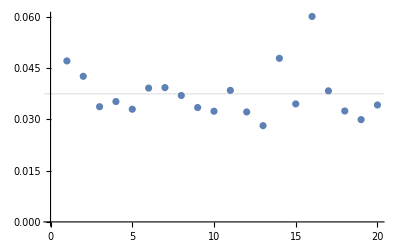
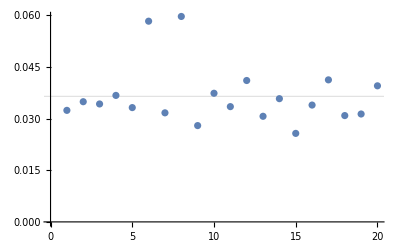

```mathematica
Table[ListPlot[prs[[conditionIdx]],GridLines->{{}, {Mean[prs[[conditionIdx]]]}}],{conditionIdx,Length[freqs]}]
```

```mathematica
rotationEv=Inverse[Transpose[Eigenvectors[connectivity]]];
statesRotatedAll=Table[Table[rotationEv.statesLabeledAll[[conditionIdx,instanceIdx,1]],{instanceIdx,instanceN}],{conditionIdx,Length[freqs]}];
prsRotated=Table[Table[0,instanceN],Length[freqs]];
Do[Do[prsRotated[[conditionIdx,instanceIdx]]=participationRatio[Map[Variance,statesRotatedAll[[conditionIdx,instanceIdx]]]],
{instanceIdx,instanceN}],{conditionIdx,Length[freqs]}]
prsNatural=Table[Table[0,instanceN],Length[freqs]];
Do[Do[prsNatural[[conditionIdx,instanceIdx]]=participationRatio[Map[Variance,statesLabeledAll[[conditionIdx,instanceIdx,1]]]],
{instanceIdx,instanceN}],{conditionIdx,Length[freqs]}]
```

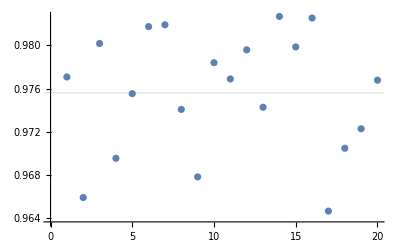
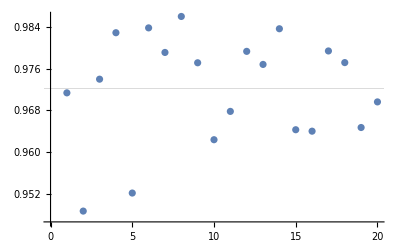
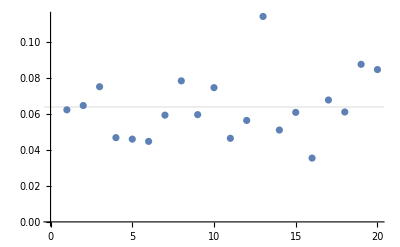
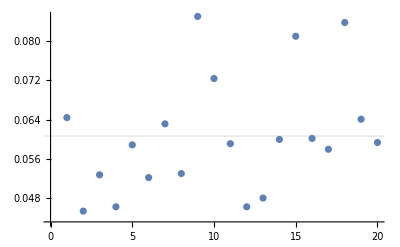
| 4/25 | 8/25
natural | -Graphics- | -Graphics-
ev | -Graphics- | -Graphics-

```mathematica
Grid[{Join[{" "},freqs],
Join[{"natural"},Table[ListPlot[prsNatural[[conditionIdx]],GridLines->{{}, {Mean[prsNatural[[conditionIdx]]]}}],{conditionIdx,Length[freqs]}]],Join[{"ev"},Table[ListPlot[prsRotated[[conditionIdx]],GridLines->{{}, {Mean[prsRotated[[conditionIdx]]]}}],{conditionIdx,Length[freqs]}]]}]
```

#### classifiability - different connectivityExternals

```mathematica
totN=100(*300*);
eR=0.8;
means={0.18};
gains=Table[5.,2];
connectivity=connectivityEI[totN,eR,means,Table[gains,2]];
externalR=0.2;
connectivityExternals=Table[Join[RandomVariate[BernoulliDistribution[externalR],Round[totN*eR]],Table[0,totN-Round[totN*eR]]],2]*1.;
nonlinearity1=Identity;
nonlinearity2=(*With[{r=0.1},Function[x,If[x>0,(2-r)Tanh[x/(2-r)],r*Tanh[x/r]]]]*)Tanh;
velocities[positions_]:=-positions+nonlinearity1[connectivity.nonlinearity2[positions]];
freq=8/50;
externalStrength=5.;
timeI={0,50};
resolution=24(*60*);
instanceN=20(*100*);
statesLabeledAll=Table[Table[(Table[Table[0,(timeI[[2]]-timeI[[1]])*resolution+1],totN]->0),instanceN],Length[connectivityExternals]];
Do[spikeTimes=Sort[RandomVariate[UniformDistribution[timeI],Round[(timeI[[2]]-timeI[[1]])*freq]]];
externals[time_]:=connectivityExternals[[conditionIdx]]*externalStrength*Total[Exp[-(time-spikeTimes)^2/2/0.5^2]];
Do[initials=RandomVariate[NormalDistribution[0,1],totN]+Table[0.,{idx,totN}];statesLabeledAll[[conditionIdx,instanceIdx]]=(nonlinearity2[rk4OdeXSolver[velocities,externals,initials,timeI,resolution]]->conditionIdx)
,{instanceIdx,instanceN}],{conditionIdx,Length[connectivityExternals]}]
Print[StringJoin["spectral radius is ",ToString[Sqrt[eR*gains[[1]]^2+(1-eR)*gains[[2]]^2]]]]
Print["external connectivity overlap is"]
Print[TableForm[connectivityExternals.Transpose[connectivityExternals]/Round[totN*eR]]]
(*save[{connectivity,connectivityExternals},"connectivities"]
save[statesLabeledAll,"statesLabeledAll"]*)
```

spectral radius is 5.

external connectivity overlap is

0.225 | 0.05
0.05 | 0.2375

%diff between rms rates: 0.0037772

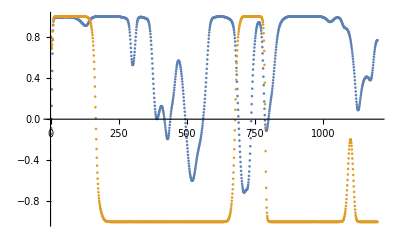
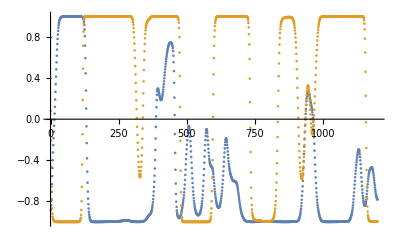

```mathematica
characteristicIdxs=Table[{Position[connectivityExternals[[conditionIdx]],0.][[1,1]],Position[connectivityExternals[[conditionIdx]],1.][[1,1]]},{conditionIdx,Length[connectivityExternals]}];
With[{means=Table[Sqrt[Mean[Mean[Mean[statesLabeledAll[[conditionIdx,;;,1]]^2]]]],{conditionIdx,Length[connectivityExternals]}]},
With[{mean1=Max[means],mean2=Min[means]},Print[StringJoin["%diff between rms rates: ",ToString[2(mean1-mean2)/(mean1+mean2)]]]]]
Table[ListPlot[statesLabeledAll[[conditionIdx,1,1]][[characteristicIdxs[[conditionIdx]]]]],{conditionIdx,Length[connectivityExternals]}]
```

```mathematica
trainingInstanceN=Round[instanceN*0.5];
classifier=Classify[Flatten[statesLabeledAll[[;;,1;;trainingInstanceN]],1](*,Method->"SupportVectorMachine"*)];
testResults=Table[Table[{statesLabeledAll[[conditionIdx,instanceIdx,2]],classifier[statesLabeledAll[[conditionIdx,instanceIdx,1]]]},{instanceIdx,trainingInstanceN+1,instanceN}],{conditionIdx,Length[connectivityExternals]}];
```

```mathematica
errors=Table[Table[{conditionIdx,testResults[[conditionIdx,instanceIdx,2]]-testResults[[conditionIdx,instanceIdx,1]]},{instanceIdx,instanceN-trainingInstanceN}],{conditionIdx,Length[connectivityExternals]}];
errorRates=Table[{conditionIdx,Mean[Map[Function[x,Boole[x≠0]],errors[[conditionIdx,;;,2]]]]},{conditionIdx,Length[connectivityExternals]}];
```

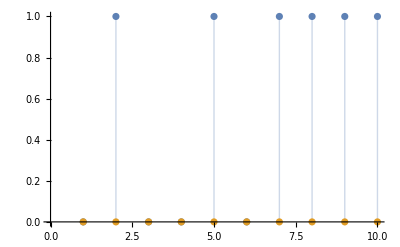
{Classifier information
Data type | NumericalTensor (size: ××1001201)
Classes | ,,12
Accuracy | (80.5.) %
Method | LogisticRegression
Single evaluation time | 2.67 s/example
Batch evaluation speed | 0.418 examples/s
Loss | 0.434 ± 0.042
Model memory | 54. MB
Training examples used | 20 examples
Training time | 1 48,class | %error
1 | 3/5
2 | 0,-Graphics-}

```mathematica
{Information[classifier],Grid[Join[{{"class","%error"}},errorRates]](*ListPlot[errorRates,Filling->Axis,PlotRange->{0,1}]*),ListPlot[errors[[;;,;;,2]],Filling->Axis]}
```

```mathematica
prs=Table[Table[0,instanceN],Length[connectivityExternals]];
Do[Do[prs[[conditionIdx,instanceIdx]]=participationRatio[Map[Variance,Transpose[PrincipalComponents[Transpose[statesLabeledAll[[conditionIdx,instanceIdx,1]]]]]]],
{instanceIdx,instanceN}],{conditionIdx,Length[connectivityExternals]}]
```

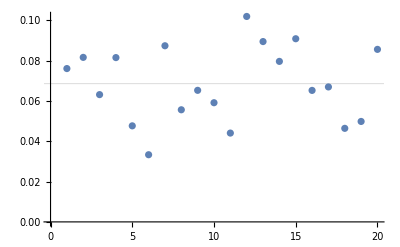
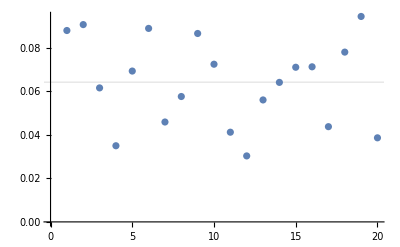

```mathematica
Table[ListPlot[prs[[conditionIdx]],GridLines->{{}, {Mean[prs[[conditionIdx]]]}}],{conditionIdx,Length[connectivityExternals]}]
```

```mathematica
rotationEv=Inverse[Transpose[Eigenvectors[connectivity]]];
statesRotatedAll=Table[Table[rotationEv.statesLabeledAll[[conditionIdx,instanceIdx,1]],{instanceIdx,instanceN}],{conditionIdx,Length[connectivityExternals]}];
prsRotated=Table[Table[0,instanceN],Length[connectivityExternals]];
Do[Do[prsRotated[[conditionIdx,instanceIdx]]=participationRatio[Map[Variance,statesRotatedAll[[conditionIdx,instanceIdx]]]],
{instanceIdx,instanceN}],{conditionIdx,Length[connectivityExternals]}]
prsNatural=Table[Table[0,instanceN],Length[connectivityExternals]];
Do[Do[prsNatural[[conditionIdx,instanceIdx]]=participationRatio[Map[Variance,statesLabeledAll[[conditionIdx,instanceIdx,1]]]],
{instanceIdx,instanceN}],{conditionIdx,Length[connectivityExternals]}]
```

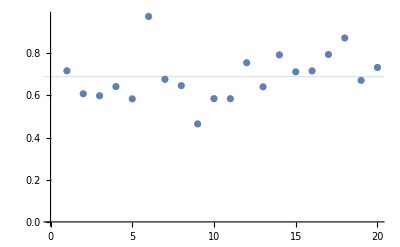
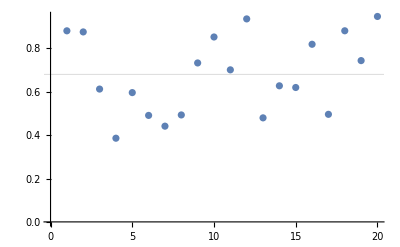
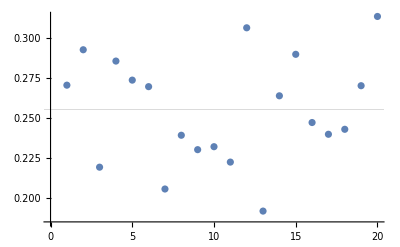
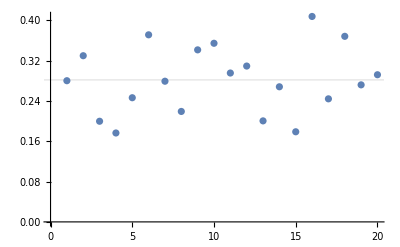
| 1 | 2
natural | -Graphics- | -Graphics-
ev | -Graphics- | -Graphics-

```mathematica
Grid[{Join[{" "},Table[idx,{idx,Length[connectivityExternals]}]],
Join[{"natural"},Table[ListPlot[prsNatural[[conditionIdx]],GridLines->{{}, {Mean[prsNatural[[conditionIdx]]]}}],{conditionIdx,Length[connectivityExternals]}]],Join[{"ev"},Table[ListPlot[prsRotated[[conditionIdx]],GridLines->{{}, {Mean[prsRotated[[conditionIdx]]]}}],{conditionIdx,Length[connectivityExternals]}]]}]
```